{{2.,5.73},{4.,11.46},{6.,17.2},{8.,22.93},{10.,28.68}}

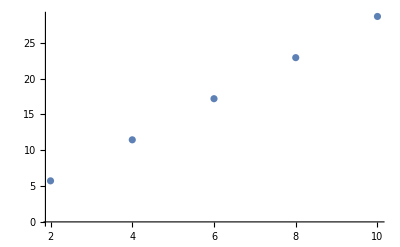

```mathematica
I1={2.00,4.00,6.00,8.00,10.00};
U1={5.73,11.46,17.20,22.93,28.68};
data1=Table[{I1[[i]],U1[[i]]},{i,1,5}]
pd=ListPlot[data1]
```

```mathematica
fd=Fit[data1,{1,x},x]
```

```mathematica
-0.01100000000002039+2.868500000000003 x
```

```mathematica
Needs["LinearRegression`"]
```

General::obspkg: "LinearRegression`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

RegressionReport::shdw: Symbol "RegressionReport" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

RSquared::shdw: Symbol "RSquared" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

Regress::shdw: Symbol "Regress" appears in multiple contexts {"LinearRegression`", "Global`"}; definitions in context "LinearRegression`" may shadow or be shadowed by other definitions.

```mathematica
Regress[data1,{1,x},x,RegressionReport->{RSquared}]
```

```mathematica
{RSquared->0.9999996657873835}
```

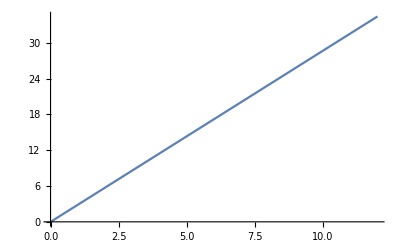

```mathematica
Plot[fd,{x,0,12}]
```

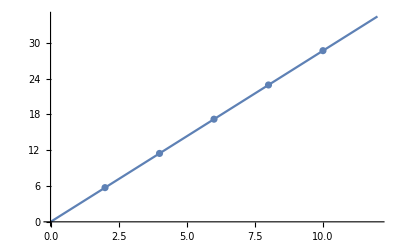

```mathematica
Show[%,pd]
```

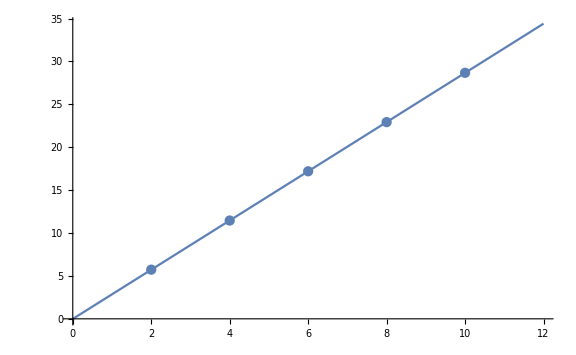

```mathematica
Show[%15,ImageSize->Large]
```

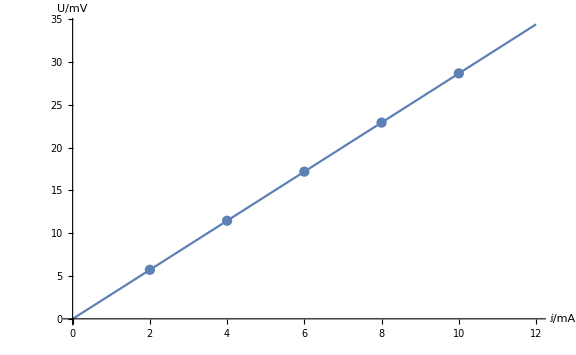

```mathematica
Show[%16,AxesLabel->{HoldForm[I/mA],HoldForm[U/mV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

{5.74,11.48,17.23,22.96,28.73}

{{2.,5.74},{4.,11.48},{6.,17.23},{8.,22.96},{10.,28.73}}

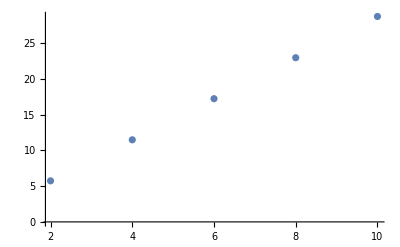

```mathematica
U2={5.74,11.48,17.23,22.96,28.73}
data2=Table[{I1[[i]],U2[[i]]},{i,1,5}]
pd2=ListPlot[data2]
```

```mathematica
{5.74,11.48,17.23,22.96,28.73}
```

{5.74,11.48,17.23,22.96,28.73}

```mathematica
fd2=Fit[data2,{1,x},x]
```

```mathematica
-0.010000000000022291+2.8730000000000033 x
```

```mathematica
Regress[data2,{1,x},x,RegressionReport->{RSquared}]
```

```mathematica
{RSquared->0.9999990307890455}
```

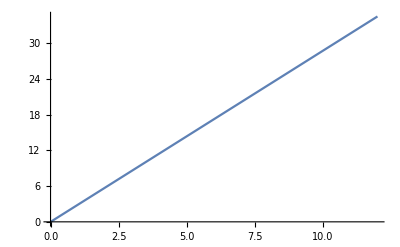

```mathematica
Plot[fd2,{x,0,12}]
```

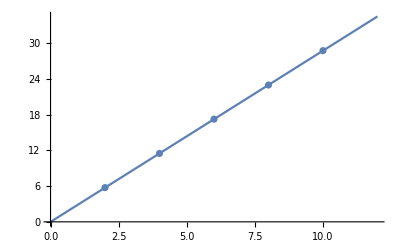

```mathematica
Show[%,pd2]
```

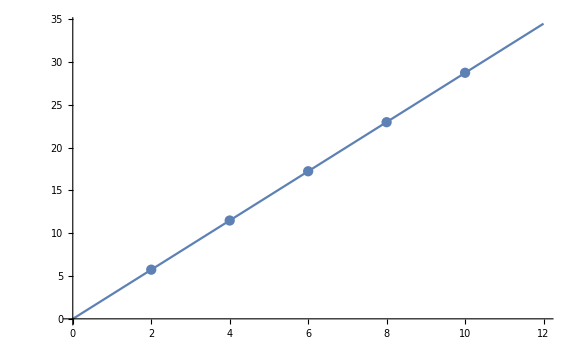

```mathematica
Show[%30,ImageSize->Large]
```

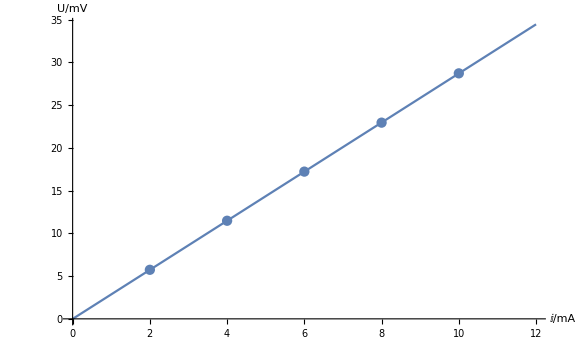

```mathematica
Show[%31,AxesLabel->{HoldForm[ⅈ/mA],HoldForm[U/mV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

{-0.21,4.87,9.59,14.39,19.12,23.87,28.69,33.5,38.32,43.14,47.89}

{-1.1,38.9,75.5,113.3,150.9,188.,226.3,264.2,303.5,340.,378.2}

{{-1.1,-0.21},{38.9,4.87},{75.5,9.59},{113.3,14.39},{150.9,19.12},{188.,23.87},{226.3,28.69},{264.2,33.5},{303.5,38.32},{340.,43.14},{378.2,47.89}}

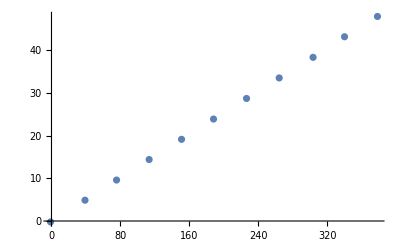

{{-1.1,-0.21},{38.9,4.87},{75.5,9.59},{113.3,14.39},{150.9,19.12},{188.,23.87},{226.3,28.69},{264.2,33.5},{303.5,38.32},{340.,43.14},{378.2,47.89}}

```mathematica
U2={-0.21,4.87,9.59,14.39,19.12,23.87,28.69,33.50,38.32,43.14,47.89}
B={-1.1,38.9,75.5,113.3,150.9,188.0,226.3,264.2,303.5,340.0,378.2}
data30=Table[{B[[i]],U2[[i]]},{i,1,11}]
pd3=ListPlot[data30]
data3=Table[{B[[i]],U2[[i]]},{i,1,11}]
```

```mathematica
fd3=Fit[data3,{1,x},x]
```

-0.0165588+0.126752 x

```mathematica
Needs["LinearRegression`"]
```

General::obspkg: "LinearRegression`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

RegressionReport::shdw: Symbol "RegressionReport" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

RSquared::shdw: Symbol "RSquared" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

Regress::shdw: Symbol "Regress" appears in multiple contexts {"LinearRegression`", "Global`"}; definitions in context "LinearRegression`" may shadow or be shadowed by other definitions.

```mathematica
Regress[data3,{1,x},x,RegressionReport->{RSquared}]
```

```mathematica
{RSquared->0.9999860650436841}
```

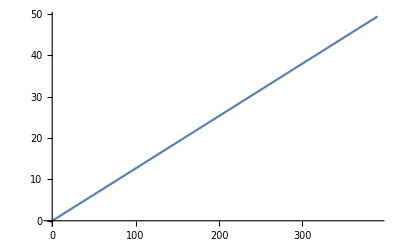

```mathematica
Plot[fd3,{x,-2,390}]
```

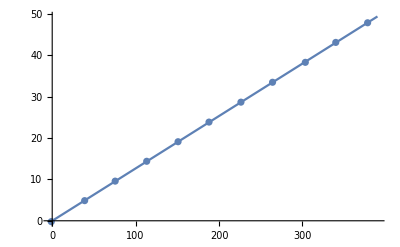

```mathematica
Show[%,pd3]
```

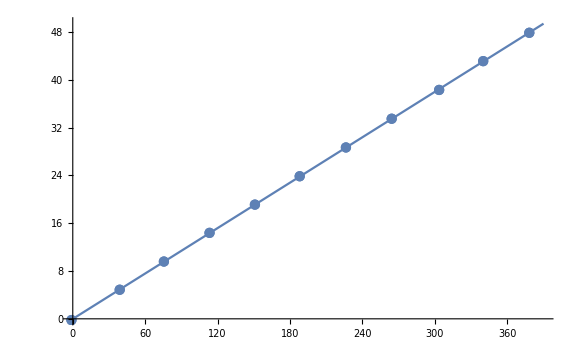

```mathematica
Show[%53,ImageSize->Large]
```

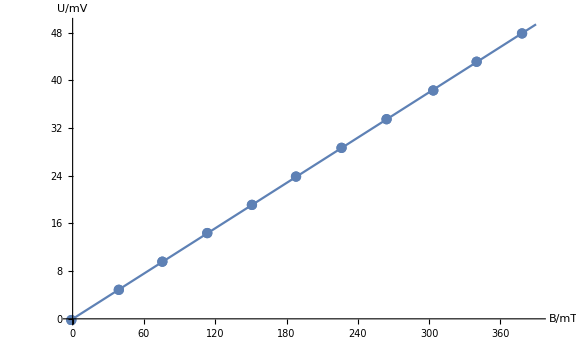

```mathematica
Show[%57,AxesLabel->{HoldForm[B/mT],HoldForm[U/mV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
I4={0.000,0.100,0.200,0.300,0.400,0.500,0.600,0.700,0.800,0.900,1.000}
B4={-1.6,38.4,75.6,113.5,150.8,188.2,226.3,264.2,302.2,340.2,377.7}
data4=Table[{I4[[i]],B4[[i]]},{i,1,11}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{-1.6,38.4,75.6,113.5,150.8,188.2,226.3,264.2,302.2,340.2,377.7}

{{0.,-1.6},{0.1,38.4},{0.2,75.6},{0.3,113.5},{0.4,150.8},{0.5,188.2},{0.6,226.3},{0.7,264.2},{0.8,302.2},{0.9,340.2},{1.,377.7}}

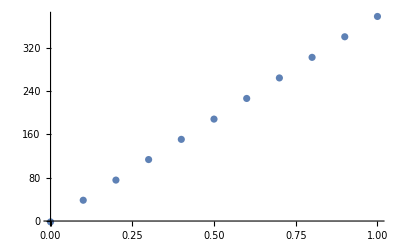

```mathematica
pd4=ListPlot[data4]
```

```mathematica
fd4=Fit[data4,{1,x},x]
```

-0.427273+378.218 x

```mathematica
Regress[data4,{1,x},x,RegressionReport->{RSquared}]
```

```mathematica
{RSquared->0.9999802741532203}
```

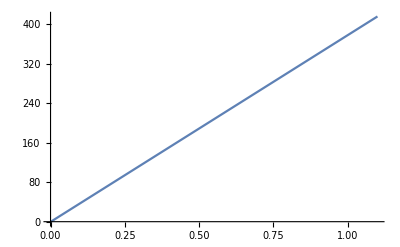

```mathematica
Plot[fd4,{x,0,1.1}]
```

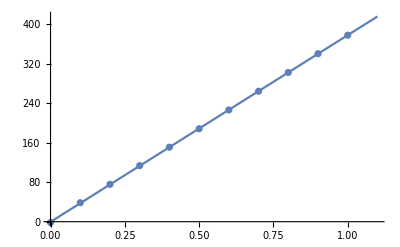

```mathematica
Show[%,pd4]
```

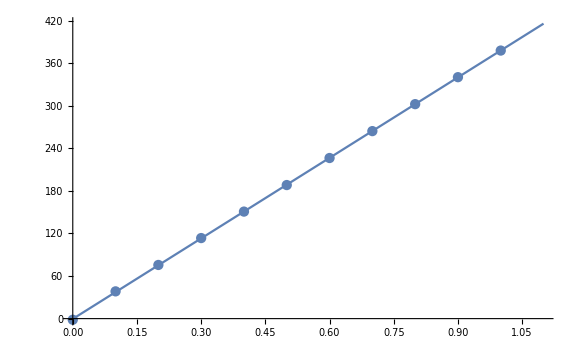

```mathematica
Show[%71,ImageSize->Large]
```

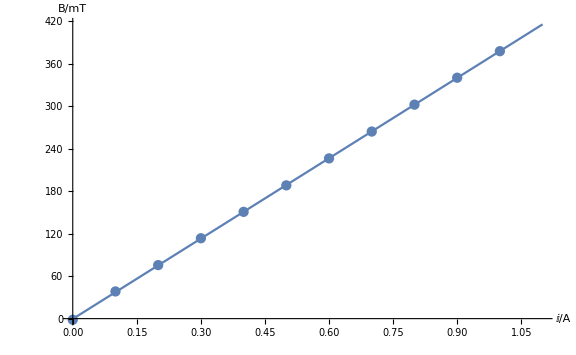

```mathematica
Show[%72,AxesLabel->{HoldForm[ⅈ/A],HoldForm[B/mT]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,25.,29.,35.,40.,45.,46.,47.,48.,49.,50.,51.}

{50.5,54.3,61.5,70.9,82.,100.6,125.3,163.,214.3,234.4,234.4,229.9,227.1,226.,225.5,225.3,225.2,225.2,225.2,225.2,225.3,225.3,225.4,225.4,225.6,225.8,226.,226.,227.9,230.6,227.4,201.5,156.9,115.9,90.62}

{{0.,50.5},{1.,54.3},{2.,61.5},{3.,70.9},{4.,82.},{5.,100.6},{6.,125.3},{7.,163.},{8.,214.3},{9.,234.4},{10.,234.4},{11.,229.9},{12.,227.1},{13.,226.},{14.,225.5},{15.,225.3},{16.,225.2},{17.,225.2},{18.,225.2},{19.,225.2},{20.,225.3},{21.,225.3},{22.,225.4},{23.,225.4},{25.,225.6},{29.,225.8},{35.,226.},{40.,226.},{45.,227.9},{46.,230.6},{47.,227.4},{48.,201.5},{49.,156.9},{50.,115.9},{51.,90.62}}

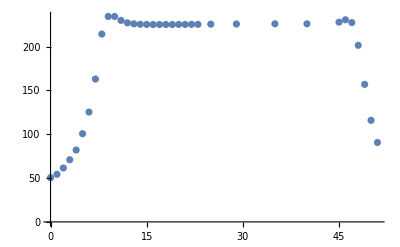

```mathematica
X={0.0,1.0,2.0,3.0,4.0,5.0,6.0,7.0,8.0,9.0,10.0,11.0,12.0,13.0,14.0,15.0,16.0,17.0,18.0,19.0,20.0,21.0,22.0,23.0,25.0,29.0,35.0,40.0,45.0,46.0,47.0,48.0,49.0,50.0,51.0}
B5={50.5,54.3,61.5,70.9,82.0,100.6,125.3,163.0,214.3,234.4,234.4,229.9,227.1,226.0,225.5,225.3,225.2,225.2,225.2,225.2,225.3,225.3,225.4,225.4,225.6,225.8,226.0,226.0,227.9,230.6,227.4,201.5,156.9,115.9,90.62}
data5=Table[{X[[i]],B5[[i]]},{i,1,35}]
pd5=ListPlot[data5]
```

```mathematica
fd5=Interpolation[data5]
```

InterpolatingFunction[{{0., 51.}}, <>]

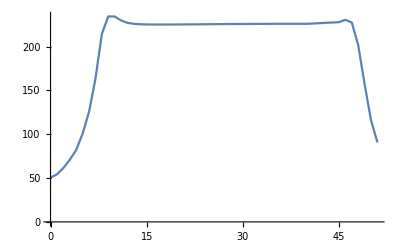

```mathematica
pd51=ListLinePlot[data5]
```

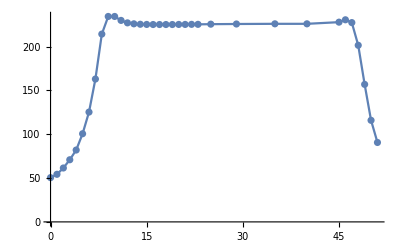

```mathematica
Show[pd51,pd5]
```

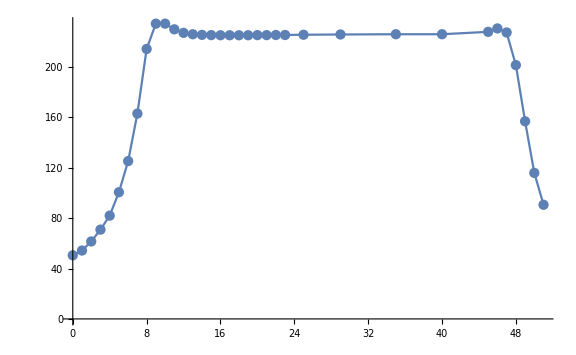

```mathematica
Show[%86,ImageSize->Large]
```

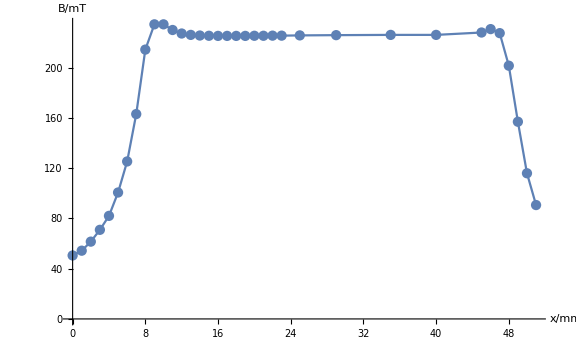

```mathematica
Show[%87,AxesLabel->{HoldForm[x/mm],HoldForm[B/mT]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```